```mathematica
initialSeedPoly[exp_,x_]:=Expand[exp/.{x->(x-Coefficient[exp,x^(Exponent[exp,x]-1)]/Exponent[exp,x])}];
stageTwoSeedPoly[exp_,x_]:=Expand[x^Exponent[exp,x]+Sum[-Abs[Coefficient[exp,x^i]]x^i,{i,1,Exponent[exp,x]-2}]-Abs[exp-Sum[Coefficient[exp,x^i]x^i,{i,1,Exponent[exp,x]}]]];
initialSeed[exp_,x_]:=
Do[
Clear[n,z,exp1,i,c1,flag];
i=0;
n =Exponent[exp,x];
c1=Coefficient[exp,x^(n-1)];
exp1=stageTwoSeedPoly[initialSeedPoly[exp,x],x];
While[
Not[And[(exp1/.x->i)≤0,(exp1/.x->i+1)≥0]],
i=i+1;
];
Return[Table[-c1/n+Round[i+1]Exp[I*(2Pi/n*(k-1)+Pi/2/n)],{k,1,n}]];
,1];
PACARootFinder[exp_,x_]:=If[
Exponent[exp,x]==1,
-(exp-x Coefficient[exp,x])/Coefficient[exp,x],
Do[
Clear[n1,z,z1,i,flag];
n1=Exponent[exp,x];
z =N[initialSeed[exp,x]];
While[True,
z1 = Table[z[[i]]+(exp/.x->z[[i]])/((exp/.x->z[[i]])*Sum[If[k≠i,1/(z[[i]]-z[[k]]),0],{k,1,n1}]-(D[exp,x]/.x->z[[i]])),{i,1,n1}];
flag=True;
For[i=1,i≤n1,i++,flag=And[flag,Abs[z[[i]]-z1[[i]]]<10^(-5)]];
If[flag,Break[]];
For[i=1,i≤n1,i++,z[[i]]=z1[[i]]];
];
Return[z1];
,1]];
NewPACARootFinder[exp_,x_]:=
Do[
Clear[n,cp,exp1,exp2,exp3,c0];
n=Exponent[exp,x];
cp=Coefficient[exp,x^n];
exp1=N[Expand[exp/cp]];
c0=exp1/.x->0;
(*Refining the coefficients*)
exp2=If[Abs[c0]<0.001,Sign[Re[c0]]0.001+I Sign[Im[c0]]0.001,c0]+Sum[ If[Abs[Coefficient[exp1,x^i]]<0.001,Sign[Re[Coefficient[exp1,x^i]]]0.001+I Sign[Im[Coefficient[exp1,x^i]]]0.001,Coefficient[exp1,x^i] ]*x^i,{i,1,n}];
cp=Coefficient[exp2,x^n];
exp3=SetPrecision[N[Expand[exp2/cp]],2];
Return[PACARootFinder[exp3,x]]
,1];
```

```mathematica
NewPACARootFinder[5*x^2-2,x]
```

{0.632456+2.06795×10^-25 ⅈ,-0.632456-2.06795×10^-25 ⅈ}

```mathematica
NewPACARootFinder[5*x^6.1-2.3,x]
```

{0.88047-3.57965×10^-18 ⅈ,0.453259+0.75484 ⅈ,-0.4138+0.777172 ⅈ,-0.879302-0.0453255 ⅈ,-0.4138-0.777172 ⅈ,0.453259-0.75484 ⅈ}

```mathematica
xp[exp_,x_]:=Do[
Clear[exp1,n,slnroot,i,m];
exp1=Numerator[Together[exp]];
n=Exponent[exp1,x];
slnroot = NewPACARootFinder[exp1,x];
m = 0;
For[i=1,i≤n,i++,
r=Re[slnroot[[i]]];
im=Abs[Im[slnroot[[i]]]];
If[im<10^(-3)&&m<r,m =r];
];
Return[m]
,1];
padZero[S_,j_]:=
Do[
Clear[k,l,y];
If[Length[S]<j+2,
Do[
y=S;
l=Length[S];
For[k=1,k≤j+2-l,k++,AppendTo[y,0]];
,1]
];
Return[y];
,1];
aExpression[n_,exp_,x_,W_,ω_,β_]:=
Do[
Clear[S,T,U,k,root,dexp,p,q,r,R];
root =xp[exp,x];
dexp=D[exp,x];
R=Table[1,{k,1,n+1}];
S=N[CoefficientList[Series[x^4 exp,{x,root,n}],x]];S1=padZero[S,n];
T=N[CoefficientList[Series[-2 exp root x^3+2 exp x^4-dexp root x^4+dexp x^5-2 ⅈ root x ω+2 ⅈ x^2 ω,{x,root,n}],x]];T1=padZero[T,n];
U=N[CoefficientList[Series[-root^2 W-root^2 W^2+2 root W x+2 root W^2 x-W x^2-W^2 x^2+dexp root^2 x^5 β-2 dexp root x^6 β+dexp x^7 β,{x,root,n}],x]];U1=padZero[U,n];
q=S1[[1]];r=T1[[1]];
F=Table[Table[l(l-1)S1[[k-l+1]]+l T1[[k-l+1]]+U1[[k-l+1]],{l,1,k-1}],{k,1,n+1}];
p=Table[-1/(k*(k-1)q+k r ),{k,2,n+1}];
For[k=2,k≤n+1,k++,
R[[k]]= Sum[R[[l]]F[[k]][[l]],{l,1,k-1}];
R[[k]]=Simplify[p [[k-1]]R[[k]]];
];
Return[R]
,1];
PACAGetModes[m_,exp_,x_,W_,β_]:=
Do[
Clear[exp1,CoeffList,RootCalc,ω,exp1,s,root,r];
root=xp[exp,x];
CoeffList=aExpression[m,exp,x,W,ω,β];
RootCalc=Table[(-root)^(n-1),{n,1,m+1}];
exp1=Sum[CoeffList[[n]]RootCalc[[n]],{n,1,m+1}];
s=Numerator[Together[exp1]];
r=NewPACARootFinder[s,ω];
Return[r]
,1];
```

```mathematica
start=AbsoluteTime[];
PACAGetModes[3,(1-2 M x+1/x^2/λ^2/.{M->6,λ->2}),x,0,-3]
end=AbsoluteTime[];
Print[end-start]
Clear[end,start]
```

{3.64587+5.93127 ⅈ,-3.64587+5.93127 ⅈ,0.+0.202428 ⅈ}

0.014533

```mathematica
PACAPlotModes[m_,exp_,x_,W_,β_]:= ListPlot[(Tooltip[{Re[#1],Abs[Im[#1]]}]&)/@PACAGetModes[m,exp,x,W,β],AspectRatio->1,AspectRatio->{Re[ω],Im[ω]}]
```

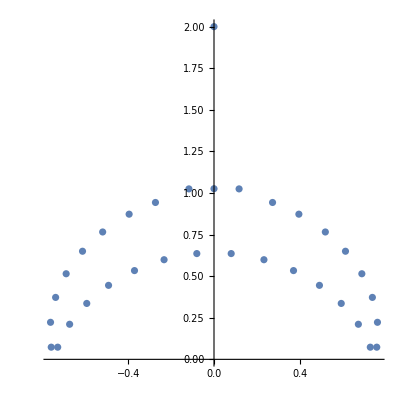

```mathematica
PACAPlotModes[34,(1-2 M x+1/x^2/l^2/.{M->6,λ->2}),x,1,1]
```

```mathematica
PACATableModes[m_,exp_,x_,W_,β_]:=
Do[
modes=PACAGetModes[m,exp,x,W,β];
rearrange=Table[{Re[modes[[k]]],Im[modes[[k]]]},{k,1,m}];
Return[TableForm[rearrange,TableHeadings->{Range[m],{"ωR","ωI"}}]]
,1];
```

```mathematica
PACATableModes[25,(1-2 M x+1/x^2/λ^2/.{M->6,λ->2}),x,1,1]
```

| ωR | ωI
1 | 0.69023 | -0.134404
2 | 0.650581 | 0.0494932
3 | 0.566556 | 0.216438
4 | -0.0998104 | 0.524136
5 | 0.4434 | 0.357703
6 | 0.285786 | 0.46365
7 | 1.21065×10^-38 | -2.
8 | -0.285786 | 0.46365
9 | -0.4434 | 0.357703
10 | 0.0998104 | 0.524136
11 | -0.566556 | 0.216438
12 | -0.650581 | 0.0494932
13 | -0.69023 | -0.134404
14 | -0.685397 | -0.323142
15 | -0.633134 | -0.50963
16 | -0.538975 | -0.676378
17 | -0.407231 | -0.825495
18 | -0.239554 | -0.934538
19 | -0.069964 | -1.02379
20 | 0.069964 | -1.02379
21 | 0.239554 | -0.934538
22 | 0.407231 | -0.825495
23 | 0.538975 | -0.676378
24 | 0.633134 | -0.50963
25 | 0.685397 | -0.323142

```mathematica
PACAShowModes[m_,exp_,x_,W_,β_]:=Print[Show[PACAPlotModes[m,exp,x,W,β],ImageSize->Large],"\t",PACATableModes[m,exp,x,W,β]]
```

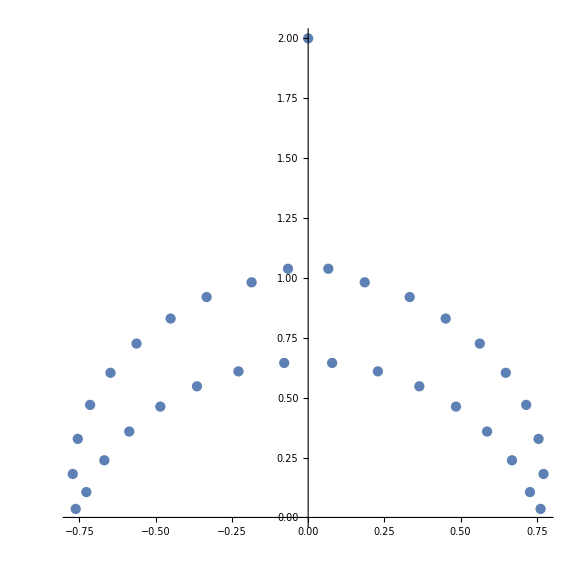
-Graphics-	 | ωR | ωI
1 | 0.772049 | -0.181508
2 | 0.762409 | -0.0357209
3 | 0.727549 | 0.105891
4 | 0.668547 | 0.238621
5 | 0.586866 | 0.358778
6 | 0.484801 | 0.462818
7 | 0.364676 | 0.547522
8 | 0.228638 | 0.609854
9 | 0.0786278 | 0.645092
10 | -0.0786278 | 0.645092
11 | -0.228638 | 0.609854
12 | -0.364676 | 0.547522
13 | -0.484801 | 0.462818
14 | -0.586866 | 0.358778
15 | -0.668547 | 0.238621
16 | -0.727549 | 0.105891
17 | -0.762409 | -0.0357209
18 | -0.772049 | -0.181508
19 | -0.755674 | -0.328079
20 | -0.715142 | -0.46991
21 | -0.648235 | -0.603944
22 | -0.562958 | -0.725841
23 | -0.451103 | -0.830371
24 | -0.333068 | -0.920123
25 | -0.185526 | -0.981585
26 | -0.0661094 | -1.03828
27 | -5.2509×10^-28 | -2.
28 | 0.0661094 | -1.03828
29 | 0.185526 | -0.981585
30 | 0.333068 | -0.920123
31 | 0.451103 | -0.830371
32 | 0.562958 | -0.725841
33 | 0.648235 | -0.603944
34 | 0.715142 | -0.46991
35 | 0.755674 | -0.328079

```mathematica
PACAShowModes[35,(1-2 M x+1/x^2/λ^2/.{M->6,λ->2}),x,1,1]
```

```mathematica
RandomReal[{0.01,12}]
```

8.94097

```mathematica
N[(μ/β)^β(β-1)^(β-1)]/.{μ->1.81,β->1.51}
```

0.93261

```mathematica
RandomReal[{0.01,Re[(μ/β)^β(β-1)^(β-1)]}]/.{μ->1.81,β->1.51}
```

RandomReal::unifr: The endpoints specified by {0.01,Re[(-1+β)^(-1+β) (μ/β)^β]} for the endpoints of the uniform distribution range are not real valued.

0.0927698

```mathematica
Sqrt[PACAGetModes[55,(1-μ x^2+Q x^(2β)/.{μ->2,β->3/2,Q->0.2}),x,1,1]]
```

{0.924124-0.0710961 ⅈ,0.919304-0.0169087 ⅈ,0.911561+0.0372131 ⅈ,0.900869+0.0911738 ⅈ,0.887294+0.144841 ⅈ,0.870871+0.198054 ⅈ,0.851637+0.250685 ⅈ,0.829646+0.302621 ⅈ,0.804962+0.353757 ⅈ,0.777635+0.404013 ⅈ,0.747696+0.453358 ⅈ,0.715098+0.501827 ⅈ,0.67956+0.549519 ⅈ,0.640217+0.596245 ⅈ,0.596245+0.640217 ⅈ,0.549519+0.67956 ⅈ,0.501827+0.715098 ⅈ,0.453358+0.747696 ⅈ,0.404013+0.777635 ⅈ,0.353757+0.804962 ⅈ,0.302621+0.829646 ⅈ,0.250685+0.851637 ⅈ,0.198054+0.870871 ⅈ,0.144841+0.887294 ⅈ,0.0911738+0.900869 ⅈ,0.0372131+0.911561 ⅈ,0.0169087-0.919304 ⅈ,0.0710961-0.924124 ⅈ,0.12509-0.926065 ⅈ,0.178751-0.924908 ⅈ,0.232257-0.920895 ⅈ,0.284766-0.914297 ⅈ,0.336557-0.903895 ⅈ,0.38865-0.891755 ⅈ,0.436876-0.876905 ⅈ,0.487262-0.856052 ⅈ,0.535642-0.840531 ⅈ,0.576126-0.811507 ⅈ,0.634702-0.787828 ⅈ,0.656297-0.766849 ⅈ,1.-1. ⅈ,0.732743-0.732743 ⅈ,0.711537-0.711537 ⅈ,0.766849-0.656297 ⅈ,0.787828-0.634702 ⅈ,0.811507-0.576126 ⅈ,0.840531-0.535642 ⅈ,0.856052-0.487262 ⅈ,0.876905-0.436876 ⅈ,0.891755-0.38865 ⅈ,0.903895-0.336557 ⅈ,0.914297-0.284766 ⅈ,0.920895-0.232257 ⅈ,0.924908-0.178751 ⅈ,0.926065-0.12509 ⅈ}

```mathematica
N[3/2]
```

1.5

```mathematica
(1-rp x-2 rp^3/R1^2x-Q^2/rp x+Q^2 x^2+1/x^2/R1^2/.{rp->50,R1->1,Q->12})
```

1+1/x^2-(6251322 x)/25+144 x^2

```mathematica
PACAGetModes[3,(1-rp x-2 rp^3/R1^2x-Q^2/rp x+Q^2 x^2+1/x^2/R1^2/.{rp->1,R1->0.5,Q->20}),x,0,0]
```

{-7289.33-11500.5 ⅈ,7289.33-11500.5 ⅈ,0.-1423.2 ⅈ}

```mathematica
Table[r,{r,1,3,1}]
```

{1,2,3}

```mathematica
Table[{50x0,Im[PACAGetModes[3,(1-rp x-2 rp^3/R1^2x-Q^2/rp x+Q^2 x^2+1/x^2/R1^2/.{rp->x0,R1->0.5,Q->10}),x,0,0]][[1]]},{x0,2,4}]
```

{{100,-4540.39},{150,-116242.},{200,-2.49647×10^6}}

```mathematica
Table[{50x0,Im[PACAGetModes[3,(1-rp x-2 rp^3/R1^2x-Q^2/rp x+Q^2 x^2+1/x^2/R1^2/.{rp->x0,R1->0.5,Q->20}),x,0,0]][[1]]},{x0,2,4}]
```

{{100,-1356.47},{150,-6015.88},{200,-63847.2}}

```mathematica
Table[{50x0,Im[PACAGetModes[3,(1-rp x-2 rp^3/R1^2x-Q^2/rp x+Q^2 x^2+1/x^2/R1^2/.{rp->x0,R1->0.5,Q->25}),x,0,0]][[1]]},{x0,2,4}]
```

{{100,-1175.74},{150,-2554.12},{200,-23034.5}}

```mathematica
N[100Sqrt[10]]
```

316.228

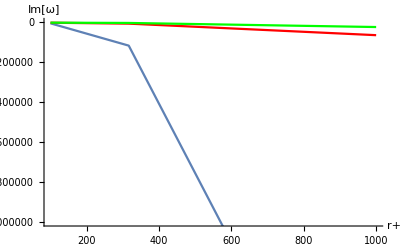

```mathematica
Block[
{},
Show[
ListLinePlot[{{100,-4540.385},{10^2.5,-116242.23},{1000,-2.496*10^6}}],
ListLinePlot[{{100,-1356.4742019999999},{10^2.5,-6015.878108},{1000,-63847.211651}},PlotStyle->Red],
ListLinePlot[{{100,-1175.738355},{10^2.5,-2554.120918},{1000,-23034.468945999997}},PlotStyle->Green],
PlotRange->{Automatic,{-10^6,0}},AxesLabel->{"r+","Im[ω]"}
]
]
```